# Off rates, run lengths and velocities as a function of load

This document compares the run lengths, velocities, and off rates of kinesin as a function of load, as measured by or stated in several papers, as well as those we use.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Bergman 2018

The parameter values we used were

```mathematica
paramvals={v->1,dstep->8,fs->5,w->2,fd->4,a->1.07,b->.186,ϵ0->.7,ϵ0a->.7,fda->4,fsa->5};
```

### Stepping rate

from my definition based on Kunwar 2011

```mathematica
kstep[f_]:=Piecewise[{{v/dstep (1-(f/fs)^w),0<f<fs},{0,f≥fs},{v/dstep,f<0}}]
```

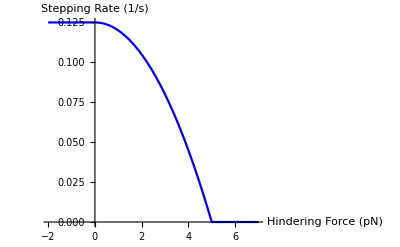

```mathematica
Plot[kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force (pN)","Stepping Rate (1/s)"},PlotStyle->Blue]
```

translate to velocity

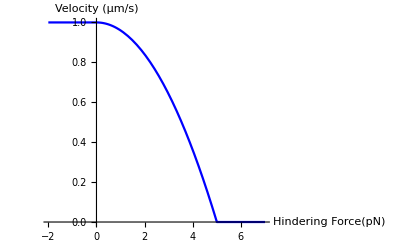

```mathematica
myvel=Plot[dstep*kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force(pN)","Velocity (μm/s)"},PlotStyle->Blue]
myvelnm=Plot[1000*dstep*kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force(pN)","Velocity (μm/s)"},PlotStyle->Blue];
```

### Run Length

My off rate, of the form from Kunwar 2011

```mathematica
koff[f_]:=Piecewise[{{ϵ0 Exp[Abs[f]/fd],f≤fs},{a+b f,f>fs}}]
```

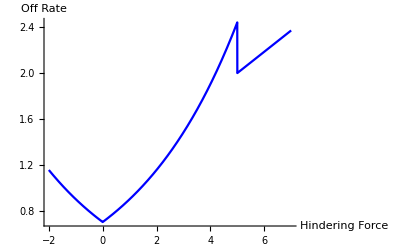

```mathematica
mykoff=Plot[koff[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force","Off Rate"},PlotStyle->Blue,PlotRange->{0,All}]
```

Then run length is

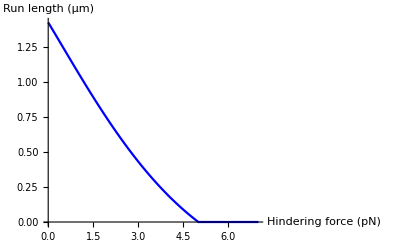

```mathematica
myrl=Plot[(dstep kstep[f])/koff[f]/.paramvals,{f,0,7},AxesLabel->{"Hindering force (pN)","Run length (μm)"},PlotStyle->Blue]
myrlnm=Plot[1000*(dstep kstep[f])/koff[f]/.paramvals,{f,0,7},AxesLabel->{"Hindering force (pN)","Run length (nm)"},PlotStyle->Blue];
```

## From Kunwar 2008 / Schnitzer 2000

Update procedure is:

-Graphics-

where

-Graphics-

Ambarish takes his run lengths and velocities from Schnizter 2000:

-Graphics-

He writes down velocity from Michaelis-Menten (supplemental equation 2):

```mathematica
v[f_]:=kcat d ϵ[f]c/(c+km[f])
```

where

```mathematica
ϵ[f_]:=1-(f/f0)^2
```

```mathematica
km[f_]:=(kcat+koff0 Exp[f dl/(kB T)])/kon
```

From this we get step probabilities, and the detachment probabilities that depend on them (supplemental equation 3-5)

```mathematica
pstep[f_]:=kcat ϵ[f] c/(c+km[f])Δt
```

```mathematica
pdetach1[f_]:=b pstep[f]/c
```

```mathematica
pdetach2[f_]:=Exp[f δl/(kB T)]pstep[f]/a
```

The run length is given as (supplemental equation 6 from Kunwar / eq. 6 from Schnitzer 2000):

```mathematica
L[f_]:=d c a Exp[-f δl/(kB T)]/(c+b(1+a Exp[-f δl/(kB T)]))
```

with the parameters

```mathematica
k2008params={d->Quantity[8,"Nanometers"],δl->Quantity[1.3,"Nanometers"],b->Quantity[.029,"Micromolar"],a->107,kB->Quantity["BoltzmannConstant"],c->Quantity[3,"Millimolar"],T->Quantity[300,"Kelvins"],
koff0->Quantity[55,1/"Seconds"],dl->Quantity[1.6,"Nanometers"],kon->Quantity[2*^6,1/("Molar"*"Seconds")],kcat->Quantity[105,1/"Seconds"],f0->Quantity[8,"Piconewtons"],Δt->Quantity[1*^-5,"Seconds"]};
```

Then we can see how the two probabilities of detachment  change with force

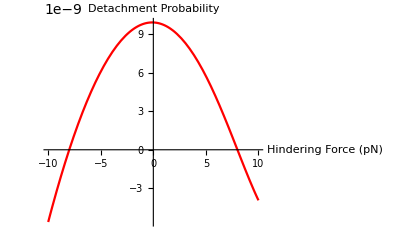

```mathematica
Plot[pdetach1[Quantity[f,"Piconewtons"]]/.k2008params,{f,-10,10},AxesLabel->{"Hindering Force (pN)","Detachment Probability"},PlotStyle->Red]
```

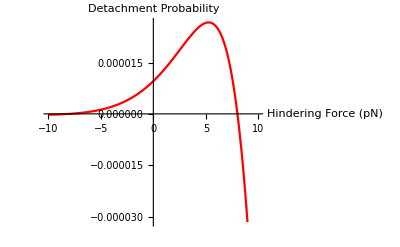

```mathematica
Plot[pdetach2[Quantity[f,"Piconewtons"]]/.k2008params,{f,-10,10},AxesLabel->{"Hindering Force (pN)","Detachment Probability"},PlotStyle->Red]
```

And the velocity

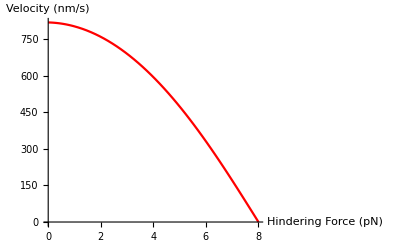

```mathematica
Svel=Plot[v[Quantity[f,"Piconewtons"]]/.k2008params,{f,0,8},PlotStyle->Red,AxesLabel->{"Hindering Force (pN)","Velocity (nm/s)"}]
```

This is different than the one we used in Bergman 2018:
our stall force was much lower
our unloaded velocity was higher

however, both are superlinear

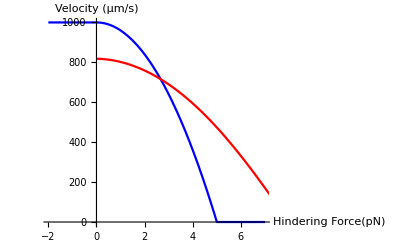

```mathematica
Show[{myvelnm,Svel}]
```

Run length as a function of force is

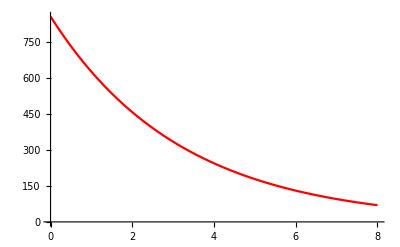

```mathematica
schnitzerrl=Plot[L[Quantity[f,"Piconewtons"]]/.k2008params,{f,0,8},PlotStyle->Red]
```

This is also different than the run length from Bergman 2018, for several reasons:
I put a hard stall at 5pN
My 0-force run lengths are longer to match Michael and Jing’s observations

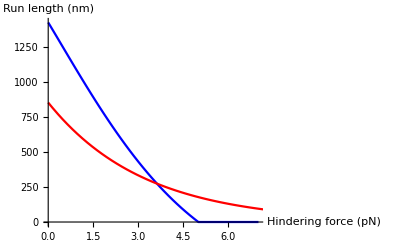

```mathematica
Show[{myrlnm,schnitzerrl}]
```

Then the effective koff in Kunwar 2008 is

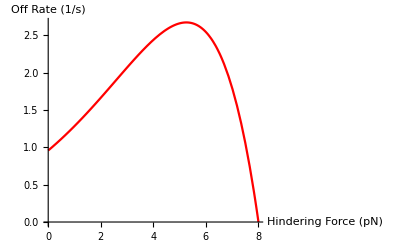

```mathematica
skoff=Plot[v[Quantity[f,"Piconewtons"]]/L[Quantity[f,"Piconewtons"]]/.k2008params,{f,0,8},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotStyle->Red]
```

which is drastically different than the off rate from Kunwar 2011 based on Gross lab measurements

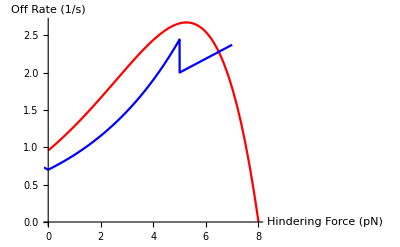

```mathematica
Show[{skoff,mykoff}]
```

To make sure we have things right, match figure S3 in Kunwar 2008

-Graphics-

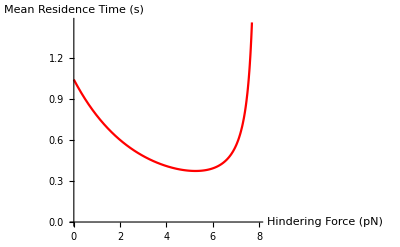

```mathematica
Plot[1/((pdetach1[Quantity[f,"Piconewtons"]]+pdetach2[Quantity[f,"Piconewtons"]])/Δt)/.k2008params,{f,0,8},AxesLabel->{"Hindering Force (pN)","Mean Residence Time (s)"},PlotStyle->Red,PlotRange->{0,Automatic}]
```

## Kunwar 2011

Update procedure is:

-Graphics-

where

-Graphics-

-Graphics-

```mathematica
Kparamvals={v->1,dstep->8,fs->5,w->2,fd->4,a->1.07,b->.186,ϵ0->1};
```

Then his off rate is (fig S5)

-Graphics-

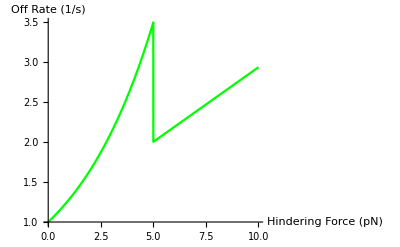

```mathematica
Plot[koff[f]/.Kparamvals,{f,0,10},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotStyle->Green]
```

but his velocity is the same as Bergman 2018, so his run lengths are

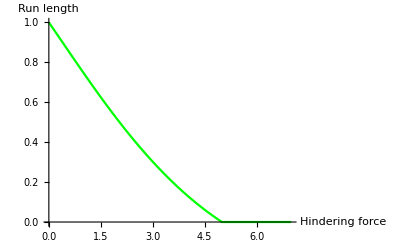

```mathematica
Krl=Plot[(dstep kstep[f])/koff[f]/.Kparamvals,{f,0,7},AxesLabel->{"Hindering force","Run length"},PlotStyle->Green]
```

Comparing to Bergman 2018

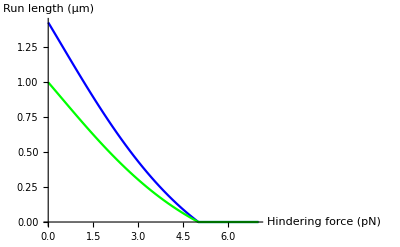

```mathematica
Show[{myrl,Krl}]
```

Unfortunately, neither Jing nor Michael have run lengths as a function of force that I can compare these to.

Data on time kinesin remains bound from Kunwar 2011 is:

Below stall, figure S2B

-Graphics-

```mathematica
k2011belowstallboundtime={{.9,1.3585069444444444},{2.7,0.5815972222222222},{4,0.3993055555555557}};
k2011belowstalloffrate=Table[{k2011belowstallboundtime[[i,1]],1/k2011belowstallboundtime[[i,2]]},{i,1,Length[k2011belowstallboundtime]}];
```

Above stall, figure 2E

-Graphics-

```mathematica
k2011abovestalltime=Import["data extracted from figures/k2011 Detachment Time.csv"];
k2011abovestalloffrate=Table[{k2011abovestalltime[[i,1]],1/k2011abovestalltime[[i,2]]},{i,1,Length[k2011abovestalltime]}];
```

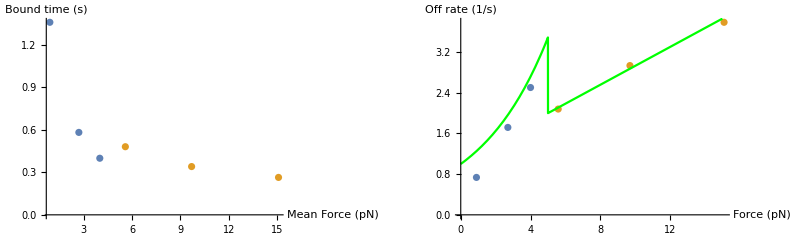

```mathematica
GraphicsRow[{ListPlot[{k2011belowstallboundtime,k2011abovestalltime},AxesLabel->{"Mean Force (pN)","Bound time (s)"},PlotRange->All],Show[ListPlot[{k2011belowstalloffrate,k2011abovestalloffrate},AxesLabel->{"Force (pN)","Off rate (1/s)"}],Plot[koff[f]/.Kparamvals,{f,0,15},PlotStyle->Green]]},ImageSize->Full]
```

## From Andreasson 2015

Andreasson gives run lengths (figure 3), velocities (figure 5), and a separate figure of off rates (figure 6), which includes off rates above stall

```mathematica
Aparamvals={ϵ0->1.11,fd->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"]/Quantity[.6,"Nanometers"],"Piconewtons"]],fsa->Infinity,fs->Infinity,ϵ0a->7.4,fda->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"]/Quantity[.32,"Nanometers"],"Piconewtons"]],
kBT->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"],"Piconewtons"*"Nanometers"]],dstep->8.2,Fi->26,k1->4900,k2->95,k3->260,δ1->4.6,δ3->.35,
l0->1120,δl->2,l0a->87,δla->.27}
```

{ϵ0→1.11,fd→6.90325,fsa→∞,fs→∞,ϵ0a→7.4,fda→12.9436,kBT→4.14195,dstep→8.2,Fi→26,k1→4900,k2→95,k3→260,δ1→4.6,δ3→0.35,l0→1120,δl→2,l0a→87,δla→0.27}

### Off Rates

From figure 6 / equation in the text

-Graphics-

-Graphics-

```mathematica
koffa[f_]:=Piecewise[{{ϵ0 Exp[Abs[f]/fd],0≤f≤fs},{a+b Abs[f],f>fs},{a+b Abs[f],f<-fsa},{ϵ0a Exp[Abs[f]/fda],0>f≥ -fsa}}]
```

#### Hindering

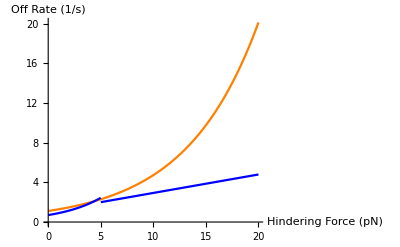

```mathematica
Aoff=Plot[koffa[f]/.{Aparamvals,paramvals}//Evaluate,{f,0,20},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotStyle->{Orange,Blue}]
```

#### Assisting

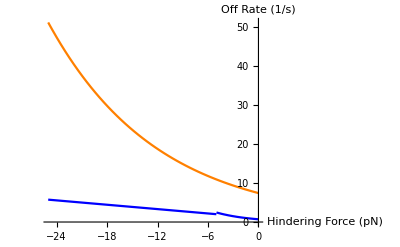

```mathematica
Plot[koffa[f]/.{Aparamvals,paramvals}//Evaluate,{f,-25,0},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotStyle->{Orange,Blue}]
```

```mathematica
hindering=Import["data extracted from figures/A2015 hindering.csv"];
hindering=Replace[hindering,{x_,y_}->{-x,y},2];
assisting=Import["data extracted from figures/A2015 assisting.csv"];
assisting=Replace[assisting,{x_,y_}->{-x,y},2];
```

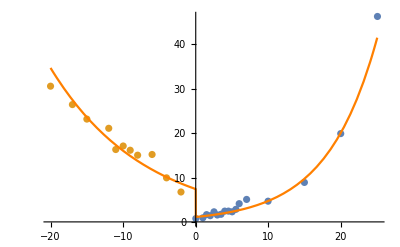

```mathematica
Show[ListPlot[{hindering,assisting}],Plot[koffa[f]/.Aparamvals//Evaluate,{f,-20,25},PlotStyle->Orange]]
```

Below stall, things compare well between theory curves

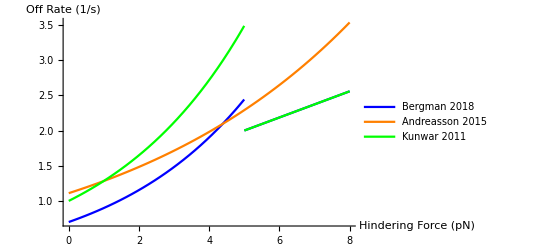

```mathematica
Plot[koff[f]/.{paramvals,Aparamvals,Kparamvals}//Evaluate,{f,0,8},PlotRange->{0,All},PlotStyle->{Blue,Orange,Green},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotLegends->{"Bergman 2018","Andreasson 2015","Kunwar 2011"}]
```

Above stall, the two measurements diverge at large forces

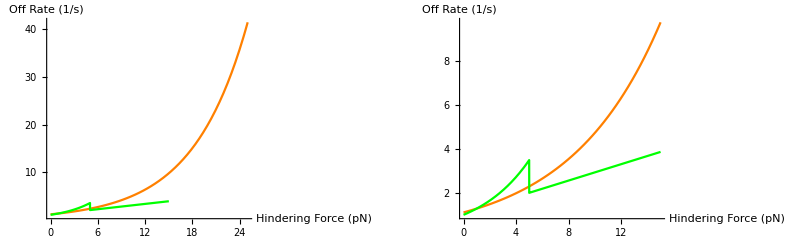

```mathematica
GraphicsRow[{Show[Plot[koffa[f]/.{Aparamvals}//Evaluate,{f,0,25},PlotRange->{0,All},PlotStyle->Orange,AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"}],
Plot[koffa[f]/.{Kparamvals}//Evaluate,{f,0,15},PlotRange->{0,All},PlotStyle->Green,AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"}]],
Show[Plot[koffa[f]/.{Aparamvals}//Evaluate,{f,0,15},PlotRange->{0,All},PlotStyle->{Blue,Orange},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"}],
Plot[koffa[f]/.{Kparamvals}//Evaluate,{f,0,15},PlotRange->{0,All},PlotStyle->{Green},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"}]]},ImageSize->Full]
```

#### Comparison between Andreasson 2015 data and Kunwar 2011 data

With the data, they actually look pretty consistent, since Gross lab only measured out to 15 pN

-Graphics--Graphics-

The measurements were done in a similar fashion. Andreasson 2015:

-Graphics-

Kunwar 2011:

-Graphics- -Graphics-

Get values from plots and and show them together

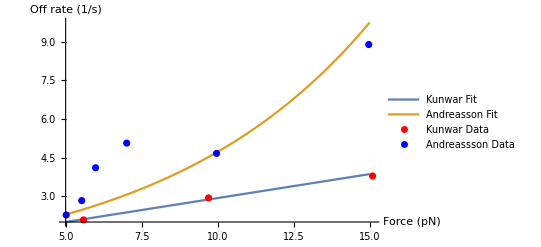

```mathematica
Show[Plot[{1.07+.186 F,koffa[F]/.Aparamvals},{F,5,15},PlotLegends->{"Kunwar Fit","Andreasson Fit"}],
ListPlot[k2011abovestalloffrate,PlotStyle->Red,PlotLegends->{"Kunwar Data"}],
ListPlot[Select[hindering,5<#[[1]]<16&],PlotStyle->Blue,PlotLegends->{"Andreassson Data"}],
PlotRange->All,AxesLabel->{"Force (pN)","Off rate (1/s)"}]
```

### Velocity

-Graphics-

From the modeling section of the paper

-Graphics-

```mathematica
vA[f_]:=dstep k1 k2 k3 Exp[(f δ1+(f+Fi)δ3)/(kBT)]/(k1 k2 Exp[f δ1/(kBT)]+k3 Exp[(f+Fi)δ3/(kBT)](k1 Exp[f δ1/(kBT)]+k2))
```

```mathematica
vA[f]
```

(dstep ⅇ^((f δ1+(f+Fi) δ3)/kBT) k1 k2 k3)/(ⅇ^((f δ1)/kBT) k1 k2+ⅇ^(((f+Fi) δ3)/kBT) (ⅇ^((f δ1)/kBT) k1+k2) k3)

My convention is negative forces are assisting, so reverse this

```mathematica
vA[f_]:=dstep k1 k2 k3 Exp[(-f δ1+(-f+Fi)δ3)/(kBT)]/(k1 k2 Exp[-f δ1/(kBT)]+k3 Exp[(-f+Fi)δ3/(kBT)](k1 Exp[-f δ1/(kBT)]+k2))
```

Data

```mathematica
a2015fv=Import["data extracted from figures/A2015 force-velocity.csv"];
a2015fv=Replace[a2015fv,{x_,y_}->{-x,y},2];
```

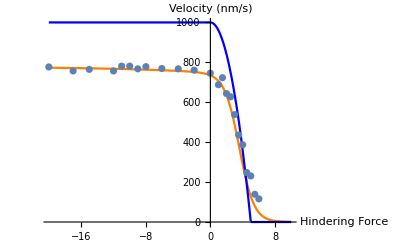

```mathematica
Show[Plot[{vA[f]/.Aparamvals,1000*dstep*kstep[f]/.paramvals}//Evaluate,{f,-20,10},PlotRange->All,PlotStyle->{Orange,Blue},AxesLabel->{"Hindering Force","Velocity (nm/s)"}],ListPlot[a2015fv]]
```

Data compares favorably to Bergman 2018 form with 770nm unhindered run length

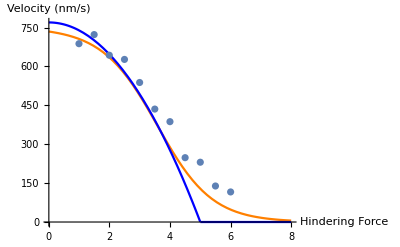

```mathematica
Show[Plot[{vA[f]/.Aparamvals,770*dstep*kstep[f]/.fs->5/.paramvals}//Evaluate,{f,0,8},PlotRange->All,PlotStyle->{Orange,Blue},AxesLabel->{"Hindering Force","Velocity (nm/s)"}],ListPlot[Select[a2015fv,#[[1]]>0&]]]
```

The only place they diverge above 5 pN. What is impact of this?

Expected travel distance at 5 pN is

```mathematica
vA[5]/koffa[5]/.Aparamvals
```

56.0923

which is 5 or 6 steps. Force at which kinesin is expected to take 5 steps before detachment:

```mathematica
Solve[5*8==vA[f]/koffa[f]/.Aparamvals,f]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{f→-12.3408},{f→5.31098}}

### Run Length

Figure 3 / table 1

-Graphics-

```mathematica
rlA[f_]:=Piecewise[{{l0a Exp[-Abs[f] δla/(kBT)],f<0},{l0 Exp[-Abs[f] δl/(kBT)],f>0}}]
```

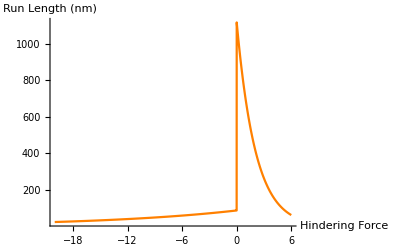

```mathematica
Plot[rlA[f]/.Aparamvals,{f,-20,6},PlotRange->{0,All},PlotStyle->Orange,AxesLabel->{"Hindering Force","Run Length (nm)"}]
```

### Derived off rate and run length

There are large differences measured quantities and their derived counterparts

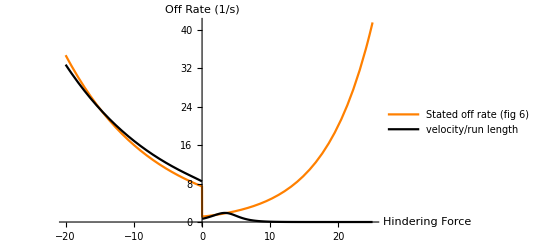

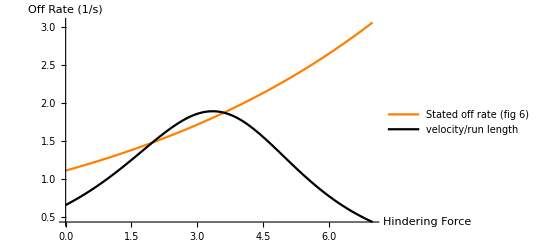

```mathematica
Plot[{koffa[f],vA[f]/rlA[f]}/.Aparamvals//Evaluate,{f,-20,25},PlotStyle->{Orange,Black},PlotLegends->{"Stated off rate (fig 6)","velocity/run length"},AxesLabel->{"Hindering Force","Off Rate (1/s)"}]
Plot[{koffa[f],vA[f]/rlA[f]}/.Aparamvals//Evaluate,{f,0,7},PlotStyle->{Orange,Black},PlotLegends->{"Stated off rate (fig 6)","velocity/run length"},AxesLabel->{"Hindering Force","Off Rate (1/s)"}]
```

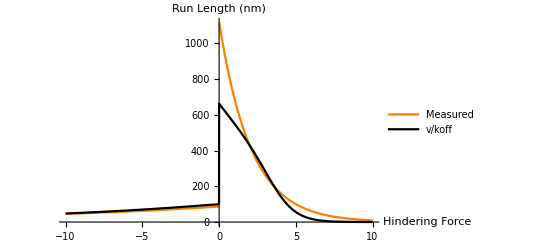

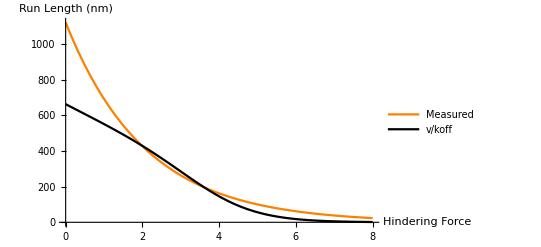

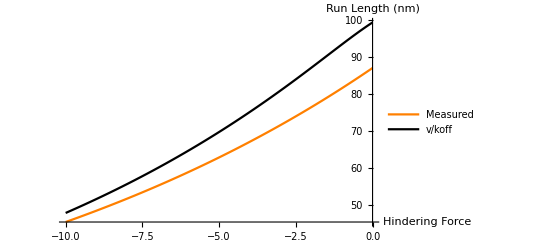

```mathematica
Plot[{rlA[f],vA[f]/koffa[f]}/.Aparamvals//Evaluate,{f,10,-10},PlotStyle->{Orange,Black},AxesLabel->{"Hindering Force","Run Length (nm)"},PlotRange->All,PlotLegends->{"Measured","v/koff"}]
Plot[{rlA[f],vA[f]/koffa[f]}/.Aparamvals//Evaluate,{f,0,8},PlotStyle->{Orange,Black},AxesLabel->{"Hindering Force","Run Length (nm)"},PlotRange->All,PlotLegends->{"Measured","v/koff"}]
Plot[{rlA[f],vA[f]/koffa[f]}/.Aparamvals//Evaluate,{f,-10,0},PlotStyle->{Orange,Black},AxesLabel->{"Hindering Force","Run Length (nm)"},PlotRange->All,PlotLegends->{"Measured","v/koff"}]
```

Perhaps a better model of off rate would solve this?

## Two rate model for off rates based on Sumi 2017

Sumi 2017 points out that a single exponential fit to the data in Andreasson 2015 isn’t great. Sumi fits a complex 8 state stepping model to the data, but says off rate is dominated by off rate from one state at low forces, but another state at high forces. I model this as two exponential rates.

-Graphics-

Plot the Sumi theory curve data together with the data from Andreasson 2015

```mathematica
theory=Import["data extracted from figures/S2017 theory.csv"];
```

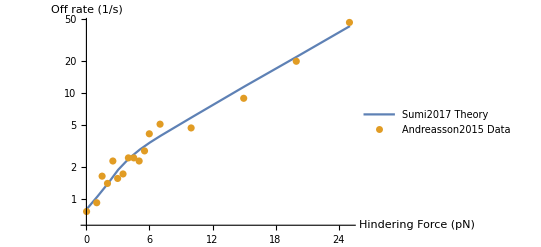

```mathematica
ListLogPlot[{theory,hindering}, AxesLabel->{"Hindering Force (pN)","Off rate (1/s)"},PlotLegends->{"Sumi2017 Theory","Andreasson2015 Data"},Joined->{True,False}]
```

Fit exponentials to the theory points on either side of 5pN

```mathematica
tnlm=NonlinearModelFit[Select[theory,#[[1]]>4.5&],a Exp[x/b],{a,b},x]
```

FittedModel[1.56307 ⅇ^(0.131966 x)]

```mathematica
tnlm["BestFitParameters"]
```

{a→1.56307,b→7.57772}

```mathematica
tnlm2=NonlinearModelFit[Select[theory,#[[1]]<4.5&],a Exp[x/b],{a,b},x]
```

FittedModel[0.798911 ⅇ^(0.27422 x)]

```mathematica
tnlm2["BestFitParameters"]
```

{a→0.798911,b→3.64671}

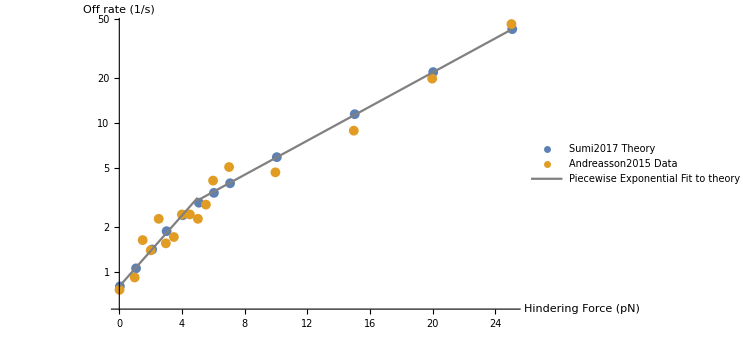

```mathematica
Show[ListLogPlot[{theory,hindering}, AxesLabel->{"Hindering Force (pN)","Off rate (1/s)"},PlotLegends->{"Sumi2017 Theory","Andreasson2015 Data"}],LogPlot[tnlm2[f],{f,0,5},PlotStyle->Gray, PlotLegends->{"Piecewise Exponential Fit to theory"}],LogPlot[tnlm[f],{f,5,25},PlotStyle->Gray],ImageSize->550]
```

The fits overestimate the theory slightly at 5pN, but are otherwise dead on.

Is this justified? What if we did the same thing with the experimental data?

```mathematica
hindSEM=Import["data extracted from figures/A2015 hindering+SEM.csv"];
SEMs=Table[{hindering[[i,1]],hindSEM[[i,2]]-hindering[[i,2]]},{i,1,Length[hindering]}];
wts=Table[hindSEM[[i,2]]-hindering[[i,2]],{i,1,Length[hindering]}];
```

```mathematica
nlm=NonlinearModelFit[Select[hindering,#[[1]]≥5&],a Exp[x/b],{a,b},x,Weights->1/(Select[SEMs,#[[1]]≥5&][[All,1]])^2,VarianceEstimatorFunction->(1&)]
```

FittedModel[1.36761 ⅇ^(0.139048 x)]

```mathematica
nlm2=NonlinearModelFit[Select[hindering,#[[1]]<5&],a Exp[x/b],{a,b},x,Weights->1/(Select[SEMs,#[[1]]<5&][[All,1]])^2,VarianceEstimatorFunction->(1&)]
```

FittedModel[0.754422 ⅇ^(0.296788 x)]

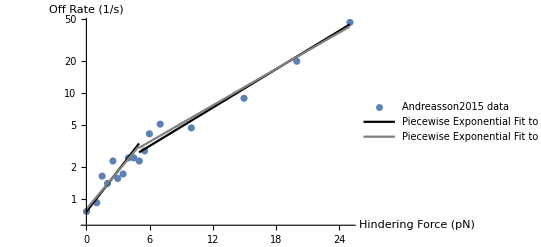

```mathematica
Show[ListLogPlot[hindering, AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotLegends->{"Andreasson2015 data"}],LogPlot[nlm2[f],{f,0,5},PlotStyle->Black,PlotLegends->{"Piecewise Exponential Fit to data"}],LogPlot[nlm[f],{f,5,25},PlotStyle->Black],LogPlot[tnlm2[f],{f,0,5},PlotStyle->Gray, PlotLegends->{"Piecewise Exponential Fit to theory"}],LogPlot[tnlm[f],{f,5,25},PlotStyle->Gray]]
```

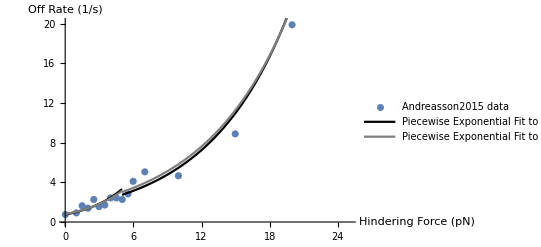

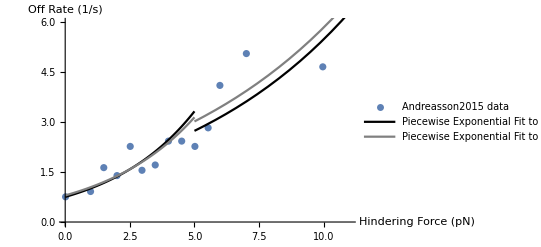

```mathematica
Show[ListPlot[hindering, AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotLegends->{"Andreasson2015 data"}],Plot[nlm2[f],{f,0,5},PlotStyle->Black,PlotLegends->{"Piecewise Exponential Fit to data"}],Plot[nlm[f],{f,5,25},PlotStyle->Black],Plot[tnlm2[f],{f,0,5},PlotStyle->Gray, PlotLegends->{"Piecewise Exponential Fit to theory"}],Plot[tnlm[f],{f,5,25},PlotStyle->Gray]]
Show[ListPlot[hindering, AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotLegends->{"Andreasson2015 data"},PlotRange->{{0,11},{0,6}}],Plot[nlm2[f],{f,0,5},PlotStyle->Black,PlotLegends->{"Piecewise Exponential Fit to data"}],Plot[nlm[f],{f,5,25},PlotStyle->Black],Plot[tnlm2[f],{f,0,5},PlotStyle->Gray, PlotLegends->{"Piecewise Exponential Fit to theory"}],Plot[tnlm[f],{f,5,25},PlotStyle->Gray]]
```

We get almost the same result either way.

## Construction of piecewise exponential off rate model

Construct a model of the form

```mathematica
newoff=Piecewise[{{ϵ1 Exp[f/fdbs],f<fs},{ϵ2 Exp[f/fdas],f>=fs}}]//Simplify
```

Piecewise[{{ⅇ^(f/fdbs) ϵ1, f<fs}, {ⅇ^(f/fdas) ϵ2, f≥fs}, {0, True}}]

ϵ1 should be the off rate at 0 force, which we’ve called ϵ0 before (equal to velocity/run length)
fdbs is the characteristic unbinding force below stall
fdas is the superstall characteristic unbinding force, it should be taken from off rate data a la Kunwar 2011/Andreasson 2015
ϵ2 is the y-intercept of the superstall exponential. There are some choices for this.

We write the base form of the off rate as

In the Andreasson case, we can independently fit these parameters to the unbinding data

### Application to Andreasson2015 data

We fit parameters to the  Andreasson 2015 data above stall.
Use velocity/run length for ϵ0 and kBT/δl for the critical unbinding force below stall

```mathematica
rls=Join[{fs->5,ϵ2->a,fdas->b}/.nlm["BestFitParameters"],
{ϵ1->vA[0]/l0,fdbs->kBT/δl}/.Aparamvals]
```

{fs→5,ϵ2→1.36761,fdas→7.19175,ϵ1→0.65617,fdbs→2.07097}

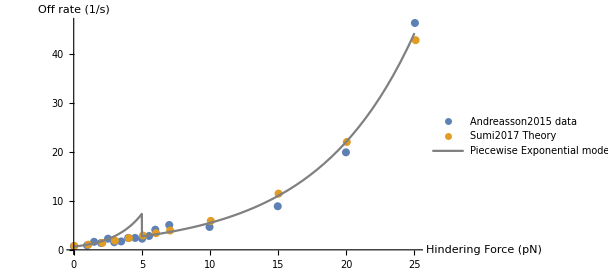

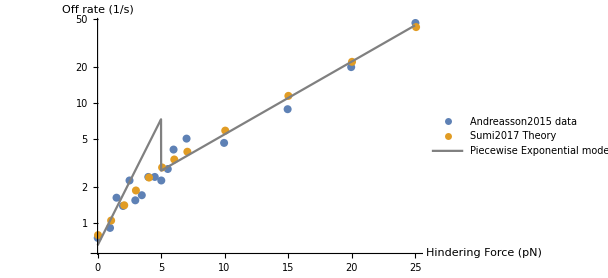

```mathematica
Show[ListPlot[{hindering,theory},PlotRange->All,AxesLabel->{"Hindering Force (pN)","Off rate (1/s)"},PlotLegends->{"Andreasson2015 data","Sumi2017 Theory"},ImageSize->450],Plot[newoff/.rls,{f,0,25},PlotStyle->Gray,PlotLegends->{"Piecewise Exponential model"}]]
Show[ListLogPlot[{hindering,theory},AxesLabel->{"Hindering Force (pN)","Off rate (1/s)"},PlotLegends->{"Andreasson2015 data","Sumi2017 Theory"},ImageSize->450],LogPlot[newoff/.rls,{f,0,25},PlotStyle->Gray,PlotLegends->{"Piecewise Exponential model"}]]
```

Looks bad at forces just below stall (not a great estimate for fdbs), but does it fix the issue?

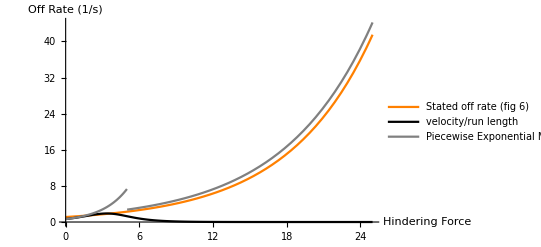

```mathematica
Plot[{koffa[f]/.Aparamvals,vA[f]/rlA[f]/.Aparamvals,newoff/.rls}//Evaluate,{f,0,25},PlotStyle->{Orange,Black,Gray},PlotLegends->{"Stated off rate (fig 6)","velocity/run length","Piecewise Exponential Model"},AxesLabel->{"Hindering Force","Off Rate (1/s)"}]
```

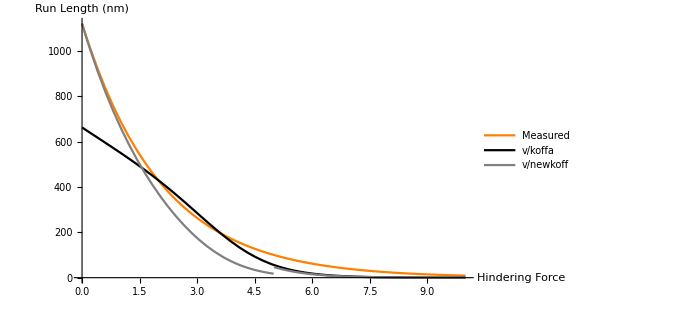

```mathematica
Plot[{rlA[f]/.Aparamvals,vA[f]/koffa[f]/.Aparamvals,vA[f]/newoff/.rls/.Aparamvals}//Evaluate,{f,0,10},PlotStyle->{Orange,Black,Gray},AxesLabel->{"Hindering Force","Run Length (nm)"},PlotRange->All,PlotLegends->{"Measured","v/koffa","v/newkoff"},ImageSize->500]
```

Things look better at low forces, but the same as the derived run length at high forces (by design). How does this compare with the data?

```mathematica
a2015rl=Import["data extracted from figures/A2015 run length.csv"];
a2015rl=Replace[a2015rl,{x_,y_}->{-x,y},2];
```

```mathematica
Manipulate[Show[Plot[{rlA[f]/.Aparamvals,vA[f]/koffa[f]/.Aparamvals,vA[f]/newoff/.{ϵ1->ϵ1m,fs->fsm,fdas->fdasm,fdbs->fdbsm,ϵ2->ϵ2m}/.Aparamvals}//Evaluate,{f,0,10},PlotStyle->{Orange,Black,Gray},AxesLabel->{"Hindering Force","Run Length (nm)"},PlotRange->All,PlotLegends->{"Measured","v/koffa","v/newkoff"},ImageSize->500],
ListPlot[a2015rl,PlotLegends->{"Andreasson2015 data"}]],{{ϵ1m,ϵ1/.rls},.5,1.2},{{fsm,fs/.rls},2,8},{{fdasm,fdas/.rls},2,12},{{fdbsm,fdbs/.rls},2,8},{{ϵ2m,ϵ2/.rls},.5,2}]
```

### Adjusting for longer 0 force run length

We could do this for the Andreasson data because run length, velocity and binding rate are measured both above and below stall. What if we only have single motor run lengths, like in Jing’s data?

First, we could assume fd1 and fd2 and force the curve to be continuous by adjusting ϵ2

```mathematica
ϵ2sol=Solve[ϵ2 Exp[fs/fdas]==ϵ1 Exp[fs/fdbs],ϵ2]//First
```

{ϵ2→ⅇ^(-fs/fdas+fs/fdbs) ϵ1}

Second, we could assume both fd2 and ϵ2 and force the curve to be continuous by adjusting fd1

```mathematica
fdbssol=Solve[ϵ1 Exp[fs/fdbs]==ϵ2 Exp[fs/fdas],fdbs]//First
```

{fdbs→ConditionalExpression[fs/(2 ⅈ π C[1]+Log[(ⅇ^(fs/fdas) ϵ2)/ϵ1]),C[1]∈ℤ]}

```mathematica
fdbssol=fdbssol/.C[1]->0
```

{fdbs→fs/Log[(ⅇ^(fs/fdas) ϵ2)/ϵ1]}

These differ in the way the curve changes when we change the unloaded run length. Let’s take the fits to the Sumi2017 theory curve as the base, then adjust ϵ1

```mathematica
rlsS=Join[{fs->5,ϵ2->a,fdas->b}/.tnlm["BestFitParameters"],
{ϵ1->a,fdbs->b}/.tnlm2["BestFitParameters"]]
```

{fs→5,ϵ2→1.56307,fdas→7.57772,ϵ1→0.798911,fdbs→3.64671}

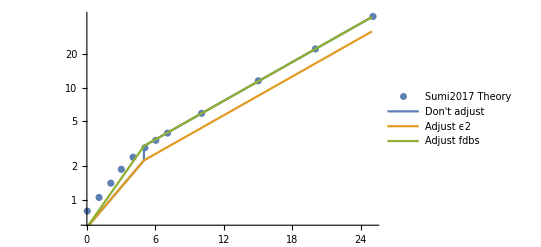

```mathematica
Show[ListLogPlot[theory,PlotLegends->{"Sumi2017 Theory"}],
LogPlot[{
newoff/.ϵ1->800/1400/.rlsS,
newoff/.ϵ2sol/.ϵ1->800/1400/.rlsS,
newoff/.fdbssol/.ϵ1->800/1400/.rlsS,
},{f,0,25},PlotLegends->{"Don't adjust","Adjust ϵ2","Adjust fdbs"}]]
```

Given that we know Jing and others measure much longer unloaded run lengths, but few others have measured as a function of force, I think the best way to stitch things together is to adjust fdbs - this gives the closest fit to the Block lab data overall.

## Full forwards & backwards off rate model

#### Hindering

```mathematica
newoff
```

Piecewise[{{ⅇ^(f/fdbs) ϵ1, f<fs}, {ⅇ^(f/fdas) ϵ2, f≥fs}, {0, True}}]

where

```mathematica
fdbssol
```

{fdbs→fs/Log[(ⅇ^(fs/fdas) ϵ2)/ϵ1]}

leading to

```mathematica
newoff/.fdbssol//Simplify
```

Piecewise[{{ϵ1 ((ⅇ^(fs/fdas) ϵ2)/ϵ1)^(f/fs), f<fs}, {ⅇ^(f/fdas) ϵ2, f≥fs}, {0, True}}]

which is sort of confusing looking

To this we plug in the parameters from Sumi2017

```mathematica
rlsS
```

{fs→5,ϵ2→1.56307,fdas→7.57772,ϵ1→0.798911,fdbs→3.64671}

which we modify by changing ϵ1 to the unloaded velocity/unloaded run length (and ignore fdbs)

#### Assisting

We’ll just use the fit from Andreasson 2015 since it looks pretty good by itself

```mathematica
Simplify[koffa[f]/.Aparamvals,f<0]
```

7.4 ⅇ^(-0.0772584 f)

#### All together:

```mathematica
Piecewise[{{v0/l0 Exp[f/fdbs]/.fdbssol,0≤f≤fs},{ϵ2 Exp[f/fd2],f>fs},{ϵa Exp[f/fda],f<0}}]
```

Piecewise[{{(v0 ((ⅇ^(fs/fdas) ϵ2)/ϵ1)^(f/fs))/l0, 0≤f≤fs}, {ⅇ^(f/fd2) ϵ2, f>fs}, {ⅇ^(f/fda) ϵa, f<0}, {0, True}}]

## Block 2003

Doesn’t seem to be any equations in the paper, so let’s just guess easy fits

```mathematica
Bparamvals={v0->668,v8r->580,v8l->430,rl0->1000,rl∞r->300,rl∞l->200,λr->.6,λl->.75}
```

{v0→668,v8r→580,v8l→430,rl0→1000,rl∞r→300,rl∞l→200,λr→0.6,λl→0.75}

Velocity looks pretty close to linear in the range of values shown

-Graphics-

```mathematica
vB[f_]:=Piecewise[{{v0-(v0-v8r)/8f,f>0},{v0-(v0-v8l)/8Abs[f],f≤0}}]
```

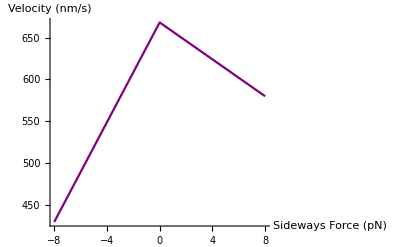

```mathematica
Plot[vB[f]/.Bparamvals,{f,-8,8},PlotRange->{0,All},PlotStyle->Purple,AxesLabel->{"Sideways Force (pN)","Velocity (nm/s)"}]
```

Run lengths look exponential

-Graphics-

```mathematica
rlB[f_]:=Piecewise[{{(rl0-rl∞r) Exp[-λr Abs[f]]+rl∞r,f≥0},{(rl0-rl∞l) Exp[-λl Abs[f]]+rl∞l,f<0}}]
```

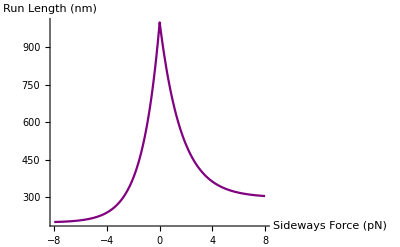

```mathematica
Plot[rlB[f]/.Bparamvals,{f,-8,8},PlotRange->{0,All},PlotStyle->Purple,AxesLabel->{"Sideways Force (pN)","Run Length (nm)"}]
```

Then we can derive an off rate

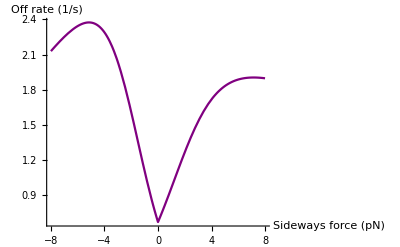

```mathematica
offrateB=Plot[vB[f]/rlB[f]/.Bparamvals,{f,-8,8},PlotRange->{0,All},PlotStyle->Purple,AxesLabel->{"Sideways force (pN)","Off rate (1/s)"}]
```

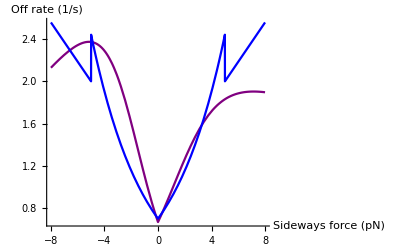

```mathematica
Plot[{vB[f]/rlB[f]/.Bparamvals,koff[Abs[f]]/.paramvals},{f,-8,8},PlotRange->{0,All},PlotStyle->{Purple,Blue},AxesLabel->{"Sideways force (pN)","Off rate (1/s)"}]
```

## Construct off rate as function of angle with MT

```mathematica
maxAngle[r_,l_]:=ArcSin[r/(r+l)]
```

```mathematica
maxAngle[.25,.08]/Degree
```

49.2509

At maxAngle backward it should look like Kunwar 2011
At maxAngle forward it should look like Andreasson 2015
At maxAngle left and right it should look like Block 2003
Michael pulled straight up in his Tau paper, but it was only an instantaneous pull and on a multiple motor cargo

Parameter values

```mathematica
ultparamvals={fd->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"]/Quantity[.6,"Nanometers"],"Piconewtons"]],fs->Infinity,ϵ0a->7.4,a->1.07,b->.186,ϵ0->.7,fsa->Infinity,ϵ0a->7.4,fda->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"]/Quantity[.32,"Nanometers"],"Piconewtons"]],
v0->668,v8r->580,v8l->430,rl0->1000,rl∞r->300,rl∞l->200,λr->.6,λl->.75}
```

{fd→6.90325,fs→∞,ϵ0a→7.4,a→1.07,b→0.186,ϵ0→0.7,fsa→∞,ϵ0a→7.4,fda→12.9436,v0→668,v8r→580,v8l→430,rl0→1000,rl∞r→300,rl∞l→200,λr→0.6,λl→0.75}

Off rate as a function of azimuthal angle

```mathematica
ultOff[f_,θ_]:=Piecewise[{{((θ-0)/(Pi/2))*koffa[-f]+((Pi/2-θ)/(Pi/2))*vB[f]/rlB[f],0<=θ<=Pi/2},
{((θ-Pi/2)/(Pi/2))*vB[-f]/rlB[-f]+((Pi-θ)/(Pi/2))*koffa[-f],Pi/2<θ<=Pi},
{((θ-Pi)/(Pi/2))*koff[f]+((3Pi/2-θ)/(Pi/2))*vB[-f]/rlB[-f],Pi<θ<=3Pi/2},
{((θ-3Pi/2)/(Pi/2))*vB[f]/rlB[f]+((2Pi-θ)/(Pi/2))*koff[f],3Pi/2<θ<=2Pi}}]
```

Off rate with azimuthal and elevation angle

```mathematica
ultOff2[f_,θ_,ϕ_]:=Piecewise[{{((ϕ-maxAngle[.25,.08])/(Pi/2-maxAngle[.25,.08]))*koff[f]+
((Pi/2-ϕ)/(Pi/2-maxAngle[.25,.08]))*ultOff[f,θ],maxAngle[.25,.08]≤ϕ≤ Pi/2},
{ultOff[f,θ],0≤ϕ< maxAngle[.25,.08]}}]
```

```mathematica
ultOff2[0,0,ϕ]
```

Piecewise[{{(1.40606 v0 (π/2-ϕ))/rl0+1.40606 (-0.859591+ϕ) (Piecewise[{{ϵ0, 0≤fs}, {a, 0>fs}, {0, True}}]), 0.859591≤ϕ≤π/2}, {v0/rl0, 0≤ϕ<0.859591}, {0, True}}]

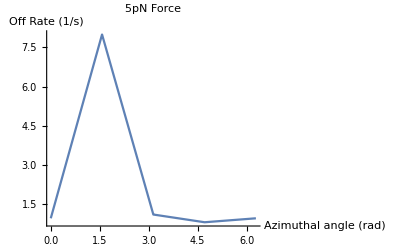

```mathematica
Plot[ultOff2[1,θ,0]/.ultparamvals,{θ,0,2Pi},AxesLabel->{"Azimuthal angle (rad)","Off Rate (1/s)"},PlotLabel-> "5pN Force",PlotRange->{0,All}]
```

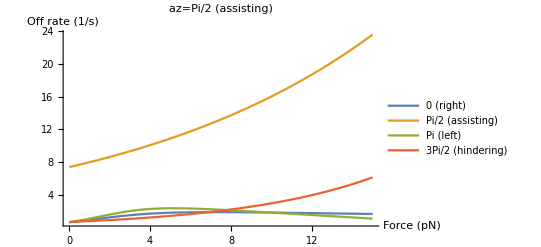

```mathematica
Plot[Evaluate[ultOff[f,#]&/@{0,Pi/2,Pi,3Pi/2}/.ultparamvals],{f,0,15},AxesLabel->{"Force (pN)","Off rate (1/s)"},PlotLabel->"az=Pi/2 (assisting)",PlotRange->{0,All},PlotLegends->{"0 (right)","Pi/2 (assisting)","Pi (left)","3Pi/2 (hindering)"}]
```

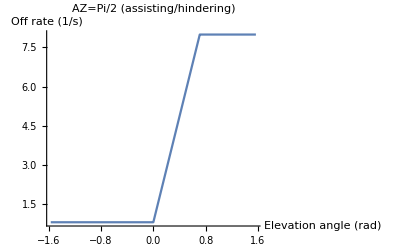

```mathematica
Plot[ultOff2[1,Piecewise[{{Pi/2,α≥0},{3Pi/2,α<0}}],Pi/2-Abs[α]]/.ultparamvals,{α,-Pi/2,Pi/2},PlotRange->{0,All},AxesLabel->{"Elevation angle (rad)","Off rate (1/s)"},PlotLabel->"AZ=Pi/2 (assisting/hindering)"]
```

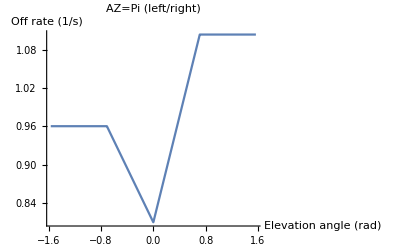

```mathematica
Plot[ultOff2[1,Piecewise[{{Pi,α≥0},{2Pi,α<0}}],Pi/2-Abs[α]]/.ultparamvals,{α,-Pi/2,Pi/2},PlotRange->{0,All},AxesLabel->{"Elevation angle (rad)","Off rate (1/s)"},PlotLabel->"AZ=Pi (left/right)"]
```

```mathematica
ParametricPlot3D[{r Cos[t],r Sin[t],ultOff[r,t]/.ultparamvals},{r,0,15},{t,0,2Pi},AxesLabel->{"Rightward Load (pN)","Assisting Load (pN)","Off Rate (1/s)"}]
```

-Graphics3D-

```mathematica
Manipulate[ParametricPlot3D[{r Cos[t],r Sin[t],ultOff2[r,t,ϕ]/.ultparamvals},{r,0,15},{t,0,2Pi},AxesLabel->{"Rightward Load (pN)","Assisting Load (pN)","Off Rate (1/s)"}],{ϕ,0,Pi/2}]
```